```mathematica
h = 6.626*10^(-34); (*J s*)
hbar = h/(2π);
e=-1.602*10^(-19); (* C *)
ϵ0=8.854*10^(-12); (* C^2/(J m) *)
me=9.109*10^(-31); (*kg*)
mp=1.673*10^(-27); (*kg*)
μ=(mp/(me+mp))*me;
a0=(4π ϵ0 hbar^2)/(μ e^2);
```

```mathematica
Ens=Table[-hbar^2/(a0^2 2 μ n^2)*1/(1.602*10^(-19)),{n,1,10}]
```

{-13.5941,-3.39852,-1.51045,-0.84963,-0.543763,-0.377613,-0.27743,-0.212408,-0.167828,-0.135941}

```mathematica
ListPlot[Ens, PlotRange->Full,AxesLabel->{"n", "E"}]
```

```mathematica
L[1,r]
```

-1

```mathematica
?Derivative
```

f' represents the derivative of a function f of one argument. 
Derivative[n_1,n_2,…][f] is the general form, representing a function obtained from f by differentiating n_1 times with respect to the first argument, n_2 times with respect to the second argument, and so on.

```mathematica
psi[n_,ρ_]:=ⅇ^-(ρ/ n)*LaguerreL[n,1,ρ]
```

```mathematica
?DensityPlot
```

DensityPlot[f,{x,x_min,x_max},{y,y_min,y_max}] makes a density plot of f as a function of x and y.

```mathematica
Export["densityplots.png",Table[DensityPlot[psi[n,Sqrt[x^2+y^2]]^2,{x,-7,7},{y,-7,7}],{n,1,6}]]
```

densityplots.png

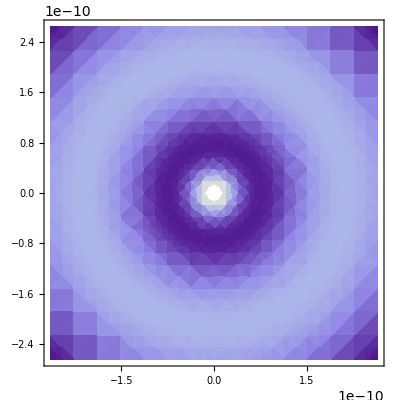

```mathematica
DensityPlot[psi[4,Sqrt[x^2+y^2]],{x,-5*a0,5*a0},{y,-5*a0,5*a0}]
```